# Towards a New Data Modelling Architecture

### By Athanassios I. Hatzis, PhD, R&D Software Engineer (C) 1st of May 2015

In Part 2 of this series we introduced the Atomic Information Resource (AIR) data model of the AtomicDB database management system. In this part we present a simple but extensive example on various representations of number three using the poweful Mathematica functions and the unique features of Mathematica notebooks. We relate these with the three-faceted abstraction mechanism in R3DM and we discuss the principles and the architectural design of R3DM, a conceptual framework based on semiosis, in Part 4.

## Part3: The number ‘3’ and The Three-Faceted Abstraction Mechanism in R3DM

Quick Introduction to Forms and In-formation

## Etymology

### Information origin

The origin of the word information reveals its use. Inform comes from the Latin verb informare, which means to give form, or to form an idea of. Where form is the mold, the container, that is used to give shape to molten, i.e. the content. At the time computer scientists were designing and constructing the first digital computer, at the same time digital information was given birth and shape. Modern computers operate with memory chips and those are mere containers of storing sequences of 0s and 1s.

### Plerophoria origin

The above interpretation and use of the word information is typical of western culture way of thinking. Although it is convenvient to keep things in boxes, Eastern philosophers used to think differently. The ancient and modern Greek word for information is πληροφορία, which transliterates (plērophoria) from πλήρης (plērēs) “fully” and φέρω (phorein) frequentative of (pherein) to carry-through. This contrasting use and interpretation of the word plerophoria traces its roots back to Socrates, Plato, and Aristotle’s theory of semiosis. In this regard every word plays the role of a symbol, i.e. sign that can be interpreted to communicate information to the one decoding that specific type of sign. There is an intimate  and inseperable connection of the signified, i.e. the concept whose meaning the interpretant attempts to decode, with the signifier, i.e. sign’s physical form such as the sound of a word. Every bit of digital information, i.e. 0 or 1 assimilates this triadic relationship. Bits are symbols signified as true or false taking the form of input voltage (signifier). The infinite combination of sequences of such symbols gives us the power to represent anything digitally. Their meaning depends on how we interpret these sequences, as numbers, letters, sounds, color, or anything else that can be encoded. The form of the signifier is not limited to that of a mere container that stores a sequence of 0s and 1s. It is a fully functional level of abstraction connected to higher and lower levels by applying recursively the theory of semiosis until we reach CPU’s binary level.

## The Turing Machine

One-tape Turing machine according to Hopcroft and Ullman can be formally defined as a 7-tuple. Elements of this tuple are members of three distinct sets. A non-empty set of tape alphabet symbols, e.g. {0, 1}, a non-empty set of states, e.g. {A, B, C, HALT} and a set of state transitions e.g. {L, R}. Turing machine reads the tape symbols and executes a sequence of instructions according to a state table. Although this is not the space and time to adapt the theory of semiosis on the Turing machine we can cleary see the role of the tape symbol as that of a sign, the signified instruction that is executed according to the interpretation given by the state table, and the physical form it takes as a printed text symbol on a white square of a paper tape. And of course you can apply the same logic to the set of states and the set of transitions because these are symbols (signs) too; they can be interpreted and realized in some other physical or non-physical form.

## Functional Representation

Functional representation is the core operation of R3DM. Everything is represented as a function that is mapping values from one domain to another. You may view functions, as transformations. This is also how they operate in Wolfram Language. They transform expressions from one symbolic form to another.

#### From bits to strings

In the following example we will see how we can apply the theory of semiosis so that it can naturally follow from the etymology of the word plerophoria as it has been discussed above.

##### The Capacitor Discharge Function

A transistor and a capacitor are paired to create a memory cell, which represents a single bit of data. When capacitor is discharged, i.e.the voltage is between zero and one Volts, we represent its state with ‘0’ and when the voltage is between two and five Volts capacitor’ s state is represented with ‘1’.

```mathematica
fCapacitor[x_]:=0/;0<x<1
fCapacitor[x_]:=1/;2<x<5
```

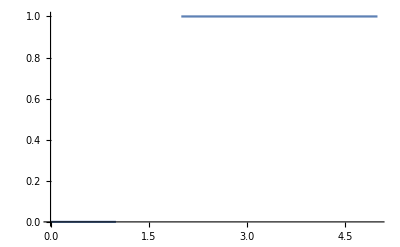

```mathematica
Plot[fCapacitor[x],{x,0,5}]
```

Notice that numbers here in the intervals {0,1} and {2,5} are interpreted as voltage values. If we want to be precise we will use the Quantity function and unit symbols in Mathematica.

```mathematica
Quantity[3,"Volt"]
```

3 V

And we will rewrite the function above to accept voltage values only.

```mathematica
fvCapacitor[v_?QuantityQ]:=0/;0<QuantityMagnitude[v]<1
fvCapacitor[v_?QuantityQ]:=1/;2<QuantityMagnitude[v]<5
```

```mathematica
fvCapacitor[3]
```

1

This is a simple but powerful example that demonstrates how a symbol, the number 3 in arabic numeral form, has been transformed, interpreted as a voltage value through the function Quantity and then how it was interpreted again as 0 or 1 through the capacitor discharge function. Let us see now how 0 and 1 can be interpreted.

##### The Transistor Switch Function

For the transistor, 1 is interpreted as the READ operation and 0 is interpreted as the CHANGE operation.

Transistor state = 1 -> Read Capacitor State
Transistor state = 0 -> Change Capacitor State

In Mathematica we can represent the above transformations with rules such as

```mathematica
{1-> READ,0->CHANGE};
```

Notice here that READ and CHANGE are symbols that have not been defined.

Or we can build another function that accepts only two values, 0 and 1 as the transistor state input and outputs symbols that represent operations on the capacitor state.

```mathematica
fTransistor[state_]:=READ/;state==1
fTransistor[state_]:=CHANGE/;state==0
```

```mathematica
{fTransistor[1],fTransistor[0]}
```

{READ,CHANGE}

We may also say that READ is represented with 1 and CHANGE with 0

##### Logic Gate Representation

A different meaning is assigned here for the same values of 0 and 1. When state is 1 that is interpreted as the logic value True and when it is 0 that is interpreted as the logic value False.

```mathematica
{1->True, 0->False};
```

Or define a function as before

```mathematica
fMemory[state_]:=True /; state==1
fMemory[state_]:=False/;state==0
```

```mathematica
{fMemory[0],fMemory[1]}
```

{False,True}

In the opposite way we can represent True and False with 1 and 0

Boole is a Wolfram Language function that transforms symbols like True to integer 1 and False to integer 0

```mathematica
{Boole[True],Boole[False]}
```

{1,0}

We may also say that True is represented with 1 and False with 0

##### Dichotomus Representation

From the examples above it becomes clear that we can assign any interpretation to a dichotomus type of variable which we assign values such as Male/Female, On/Off, Yes/No or others. In all the cases the representation can be done with ‘0’ and ‘1’ symbols and the physical realization, i.e. storage of data can also be done using the same two integers.

##### Memory Addressing and Interpretation

A memory container is defined by a starting memory address and the sequence of bits to read, memLength. This is interpreted as a memObject.

```mathematica
isMemoryFunction[memAddress,memLength]->memObject
```

isMemoryFunction[memAddress,memLength]→memObject

For example a sequence of 8 bits, byte, that is encoded here with the string

```mathematica
StringLength["01000001"]
```

8

```mathematica
FromDigits["01000001",2]
```

65

This byte is decoded in decimal system as the integer 65. And then according to ASCII coding scheme, number 65 is decoded as the character “A”. This in turn is interpreted as the capital letter “A” of the English Alphabet. Therefore this specific “A” can be represented with either an integer, or a binary number, or a character.

```mathematica
Head["A"]
```

String

```mathematica
ToCharacterCode["A"][[1]]
```

65

```mathematica
Head[%]
```

Integer

```mathematica
BaseForm[65,2]
```

1000001_2

```mathematica
Head[%]
```

Integer

Therefore in the example above we can distinguish the notion of the interpretation, e.g. “The capital letter A of the English Alphabet” as an information resource, that remains the same for any representation, i.e. the displayed form of it such as character “A”, the integer number 65, and the binary number ("1000001")_("2"). There is a third notion of the realization, i.e. the type of container that stores the value of the symbol for evaluation purposes. In the first case the character “A” is stored into a string container but the other two representations are integer expressions. The binary form of letter “A” affects printing but not evaluation as it is stored in the same way as number 65.

Now consider a 32bit representation of the number 65

```mathematica
StringLength["00000000000000000000000001000001"]
```

32

```mathematica
Head["00000000000000000000000001000001"]
```

String

```mathematica
FromDigits["00000000000000000000000001000001",2]
```

65

This 32bit representation is stored and it is evaluated as a string of digits, not as a number. It is the function FromDigits that converts the string to an integer number.

#### Building higher abstractions from primitives

##### Display Representation - VGA - compatible text mode

According to Wikipedia, “Text mode is a computer display mode in which content is internally represented on a computer screen in terms of characters rather than individual pixels”.

By far the most common text mode used in DOS environments, and initial Windows consoles, is the default 80 columns by 25 rows, or 80x25, where each character is represented by a dot matrix (a matrix of bits). The MDA (Monochrome Display Adapter) mode is using a 9x14 matrix of pixels. A pixel is is the smallest controllable element of a picture represented on the screen. The total graphics resolution of the MDA is calculated by multiplying the 80x25 matrix of characters with the 9x14 matrix of pixels which is 720x350 pixels.

Therefore, any display content can be represented on a 80x25 matrix of characters and the 80x25 matrix of characters is realized on a 720x350 matrix of pixels. The most primitive element here is the pixel and we use them to build a higher abstraction layer which is made of characters. Then a character can play the role of a fundamental unit that is used to compose words, sentences and even textual graphics.

##### Content Representation - Strings, Words, Files and Folders and Drives

Apparently there is a chain of interpretations, representations and realizations that are built in a consecutive order. This chain of semiosis reveals the mechanism that we can use to build higher levels of abstraction. At each step the symbol that is used to link together the signifier with the signified can become a fundamental unit, i.e. signifier to build the next level of abstraction. Thus we can move in two directions, we can generalize or we can specialize. In the following example we start with a generalization procedure, and we read from left to right.

Matrix of Bits (Signifier)			isSymbolizedAs→Character (Sign)		isSignifiedAs→Letter (Signified)

Sequence of Characters (Signifier) 		isSymbolizedAs→String (Sign) 		isSignifiedAs→Word (Signified)

Sequence of Strings (Signifier)		isSymbolizedAs→Sentence (Sign)		isSignifiedAs→Statement (Signified)

Sequence of Sentences (Signifier)		isSymbolizedAs→Text File (Sign)		isSignifiedAs→Document (Signified)

Collection of Text Files (Signifier)		isSymbolizedAs→Folder (Sign)		isSignifiedAs→Folded cover for holding a collection of documents (Signified)

Collection of Folders (Signifier)		isSymbolizedAs→Drive (Sign)			isSignifiedAs→Filing Cabinet (Signified)

The same example can be read backwards, i.e. from right to left if we change the linked phrases

Collection of Folders (Realization)		←isRealizedAs Drive (Representation)	←isRepresentedAs Filing Cabinet (Resource)

Collection of Text Files (Realization)		←isRealizedAs Folder (Representation)	←isRepresentedAs Folded cover for holding a collection of documents (Resource)

Sequence of Sentences (Realization)	←isRealizedAs Text File (Representation)	←isRepresentedAs Document (Resource)

Sequence of String (Realization)		←isRealizedAs Sentence (Representation)	←isRepresentedAs Statement (Resource)

Sequence of Characters (Realization)	←isRealizedAs String (Representation)	←isRepresentedAs Word (Resource)

Matrix of Bits (Realization)			←isRealizedAs Character (Representation)	←isRepresentedAs Letter (Resource)

We have constructed a uniform generalization of the abstraction mechanism with a three-faceted representation:  
Signifier-Sign-Signified (S3) or Realization-Representation-Resource (R3) based on the theory of semiosis.

## Symbolic Expressions

Everything in Wolfram Language is represented with an expression, but every expression has a head, i.e. Symbol that specifies its functionality and computability. The Basic Internal Architecture tutorial explains how crucial is the role of Wolfram Language Symbol. Every expression is structured and parsed according to the placement of symbols. 

For each Symbol, a pointer entry, i.e. a fixed computer memory address, in a central table of all symbols is defined in a Wolfram Language session. Therefore each Symbol represents a pointer that specifies an address in computer memory at which the internal representation of the actual expression is found. This memory address contains also a pointer to a string giving the symbol’s name, as well as other pointers, i.e. other Symbols, to evaluate subexpressions. The names of symbols defined by the user in a session are placed in the Global` context. We can take a list of these with the following command.

```mathematica
Names["Global`*"]
```

{CHANGE,fCapacitor,fMemory,fTransistor,fvCapacitor,isMemoryFunction,memAddress,memLength,memObject,READ,state,v,x}

Built-in Wolfram language objects are in the System` context. Therefore we can issue the following command  to remove completely any previously user-defined symbols.

```mathematica
Remove["Global`*"]
```

```mathematica
Names["Global`*"]
```

{}

Functional Representations of Number 3
The Sign - Representation

In this section we will investigate the various forms that a symbol related to number ‘3’ can take. In R3DM this is the sign that is used to signify something at a higher level and at the same time it is used to symbolize an internal representation, a realization.

## Display Format

We start our journey into the re-presentations  with the display format, i.e. something that is presented, appears on the screen with a certain form

```mathematica
BaseForm[3,2]
```

11_2

```mathematica
Subscript["11", "2"]//Head
```

Integer

Number three is displayed here in a binary format, but internally it is realized, evaluated, as an integer.

### Cell Representation

Cell is the low-level representation of a cell inside a Wolfram System notebook. In the previous examples the input of a symbol, such as Three, in a Wolfram System Notebook, is represented underneath with the string “Three”. That string is encoded in another expression, i.e. a Cell expression, that prints its content, BoxData, with a specified format. We can select “Show Expression” option from the menu Cell, or use the shortcut Shift+Ctrl+E to examine the underlying cell structure of any expression that is displayed on Input or Output Notebook cells.

```mathematica
Cell[BoxData["Three"],"Input",FontSize->24]//DisplayForm
```

Three

```mathematica
Three//Head
```

ExpressionCell

### Box Representation

The following low-level box constructs represents a textual and graphical display form of three to the power of three (3^3). These boxes are usually arranged in a nested collection that correspond to objects that are to be placed at definite relative positions in two dimensions, see “Representing Textual Forms by Boxes”,

#### SuperscriptBox of 3 to the 3 ≅3^3

```mathematica
SuperscriptBox[3,3]//StandardForm
```

SuperscriptBox[3,3]

```mathematica
%//Head
```

SuperscriptBox

Here StandardForm refers literraly to the output of the Input Cell Expression. But this specific cell expression cannot be interpreted or formatted further. Let us examine the structure of the expression underneath.

```mathematica
Cell[
BoxData[
RowBox[
{"SuperscriptBox","[",RowBox[{"3", ",", "3"}], "]"}
]
], "Output"
]//DisplayForm
```

SuperscriptBox[3,3]

```mathematica
%//Head
```

Cell

But the RawBoxes construct on the above SuperscriptBox expression prints the low-level SuperscriptBox construct in explicit two-dimensional form. Nevertheless RawBoxes IS NOT a wrapper, it affects both display and evaluation.

```mathematica
SuperscriptBox[3,3]//RawBoxes
```

3^3

```mathematica
%//Head
```

RawBoxes

The same result is printed using the DisplayForm

```mathematica
SuperscriptBox[3,3]//DisplayForm
```

3^3

```mathematica
%//Head
```

SuperscriptBox

```mathematica
Cell[BoxData[ SuperscriptBox["3", "3"]], "Input"]//DisplayForm
```

3^3

```mathematica
%//Head
```

Cell

```mathematica
%%//StandardForm
```

Cell[BoxData[SuperscriptBox[3,3]],Input]

#### Display Wrappers

Notice that in the evaluation of the expressions above, FullForm, InputForm, StandardForm, DisplayForm act as “wrappers”. They affect display but not evaluation.

### Input and Output Representations

Expressions in Wolfram language can be displayed with many formats depending on whether they are used for input or output. Normally the naming of these display formats such as InputForm or OutputForm are paired with the input and output cells that are used for entering expressions and displaying results, but they can be interchangeable. There are many ways to enter (input of) an expression, e.g. from keyboard, from a notation palette, from cutting and paste other Cell expressions. Similarly there are many ways to display a result, i.e. what an expression returns as output. 

For example, in the following input expression of √3, a two-dimensional form, we instruct the kernel to output the result using the InputForm format. Notice that this is not necessarily the format we use to enter an expression. In fact input expressions can take any form, including the InputForm of course.

```mathematica
√3//InputForm
```

Sqrt[3]

Or if we reverse the display formats, then we can use one-dimensional form for the input of the expression, i.e. use the keyboard to enter Sqrt[3] and request a standard form for the output of the expression :

```mathematica
Sqrt[3]//StandardForm
```

√3

StandardForm is the default format that is used for the output of expressions

Now, use the keyboard input form, Sqrt[3], again and format the output in a more traditional mathematical notation form :

```mathematica
Sqrt[3]//TraditionalForm
```

√3

It is important at this point to understand that the various forms, that are used for input and output of expressions, do not affect the evaluation of the expression. This is because evaluation depends always on the internal representation. FullForm, InputForm, StandardForm, DisplayForm act as display wrappers.

### 2D Low-Level Representation

We continue our discussion with more examples on the 2D display format of expressions.

#### Superscript of 3 to the 3 - (3^3)

The following expression represents a 2D object that is displayed with a proper superscript format. Notice that this expression is not interpreted as Power[3,3]. It is only formatted as 3^3 in StandardForm and DisplayForm

```mathematica
Superscript[3,3]//DisplayForm
```

3^3

If we copy and paste the previous output (3^3) into an input expression we will have

```mathematica
3^3//Defer//FullForm
```

Defer[Superscript[3,3]]

But, entering superscript notation directly, through x Ctrl + ^ y will be interpreted as Power[x, y] :

```mathematica
3^3 //Defer//FullForm
```

Defer[Power[3,3]]

Supersciptbox is the low-level representation of Superscript.

```mathematica
SuperscriptBox["3","3"]//DisplayForm
```

3^3

If we examine the previous output expression (3^3) we see that it is evaluated as a Power expression

```mathematica
3^3//Defer//FullForm
```

Defer[Power[3,3]]

and If we use a more generic low-level representation using the TemplateBox

```mathematica
TemplateBox[{"3","3"},"Superscript"]//RawBoxes
```

3^3

this time the full form of this output is a Superscipt expression

```mathematica
3^3//Defer//FullForm
```

Defer[Superscript[3,3]]

and then to print low - level boxes we can use an expression such as

```mathematica
Cell[BoxData[TemplateBox[{"3","3"},"Superscript"]],"Output"]//DisplayForm
```

3^3

But in this case the last output (3^3) is internally represented as

```mathematica
3^3//Defer//FullForm
```

Defer[ExpressionCell[Superscript[3,3],"Output"]]

With this example we see how differently the kernel evaluates 3^3 according to its internal representation

#### Power of 3 to the 3 - (3^3)

The following expression is evaluated and the integer 27 is returned as the output result.

```mathematica
3^3
```

27

We use the unevaluated form of the expression above to examine other display formats

```mathematica
Unevaluated[3^3]//FullForm
```

Unevaluated[Power[3,3]]

```mathematica
Unevaluated[3^3]//InputForm
```

Unevaluated[3^3]

```mathematica
Unevaluated[3^3]//StandardForm
```

Unevaluated[3^3]

```mathematica
Unevaluated[3^3]//DisplayForm
```

Unevaluated[3^3]

#### Square root of 3 - (3^(1/2))

The symbol “Sqrt” is intepreted as the square root. We can enter an expression such as Sqrt[3] with this input format and the Wolfram Language evaluates it and returns the result with the default output format that prints a root symbol instead of the string “Sqrt”. Both the input and output format of Sqrt[3] can be displayed by entering cell expressions.

```mathematica
Sqrt[3]
```

√3

The following cell expressions underneath are visual representations of the above input and output expressions, notice that a special SqrtBox is used to display the root symbol on a two-dimensional output format.

```mathematica
Cell[
BoxData[
 RowBox[{"Sqrt", "[", "3", "]"}]], "Input"]//DisplayForm
```

Sqrt[3]

```mathematica
Cell[
BoxData[
SqrtBox["3"]], "Output"]//DisplayForm
```

√3

```mathematica
%//InputForm
```

Cell[BoxData[\(\@3\)], "Output"]

```mathematica
%%//StandardForm
```

Cell[BoxData[SqrtBox[3]],Output]

```mathematica
%%%//FullForm
```

Cell[BoxData[SqrtBox["3"]],"Output"]

Let us print another cell expression of Sqrt[3] with a font style similar to that used in a SubSection and a Bold Font.

```mathematica
Cell[
BoxData[
SqrtBox["3"]], "Subsection",FontWeight->"Bold"]//DisplayForm
```

√3

Other display formats for the square root of 3

```mathematica
Sqrt[3]
```

√3

```mathematica
%//FullForm
```

Power[3,Rational[1,2]]

```mathematica
%//InputForm
```

Sqrt[3]

```mathematica
%//StandardForm
```

√3

```mathematica
%//TraditionalForm
```

√3

#### Multiplication 3x3

```mathematica
3 3
```

9

```mathematica
Unevaluated[3 3]//FullForm
```

Unevaluated[Times[3,3]]

```mathematica
Unevaluated[3 3]//InputForm
```

Unevaluated[3*3]

```mathematica
Cell[BoxData[RowBox[{3," ",3}]]]//DisplayForm
```

3 3

```mathematica
%//FullForm
```

Cell[BoxData[RowBox[List[3," ",3]]]]

```mathematica
%%//InputForm
```

Cell[BoxData[RowBox[{3, " ", 3}]]]

```mathematica
%%%//StandardForm
```

Cell[BoxData[RowBox[{3, ,3}]]]

## Internal Representation

Internal representation is the full functional form of an expression. Consider the square root of three, it can be displayed with the standard square root symbol such as

```mathematica
√3//FullForm
```

Power[3,Rational[1,2]]

But when we ask to see the full functional form, the kernel returns a different expression with other symbols that represent functions such as the Power and Rational.

```mathematica
√3//Head
```

Power

We can display it as a tree to visualise the structure of the expression with Symbols as Heads and Atoms as leaf nodes. This is also a nice visualization of the internal representation that is used inside the Wolfram kernel for evaluation purposes, free of any display formats, textual styles, graphics or 2D notation format.

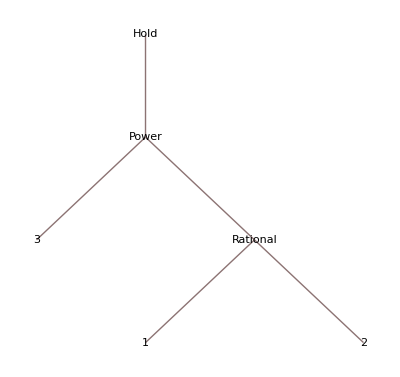

```mathematica
Hold[Power[3,Rational[1,2]]]//TreeForm
```

## String vs Symbol Representation

Let us take the string form first and apply the Head function

```mathematica
"Three"
```

Three

```mathematica
%//Head
```

String

Use a symbol now

```mathematica
Three
```

Three

```mathematica
%//Head
```

Symbol

Notice that in both cases, the output (Three) looks the same, but it is not internally. In the first case it is a string, in the second it is a symbol. The input of an expression such as Three, or three in a notebook cell is automatically recognised by Wolfram kernel as a symbol. The “Symbol” Function  refers to a symbol with the specified string name and returns the Symbol with that name. The two strings in the following list are symbolized as Three and  three

```mathematica
Symbol/@{"Three","three"}
```

{Three,three}

```mathematica
Head/@ %
```

{Symbol,Symbol}

## String vs Numeric Representation

How about entering the following list

```mathematica
{"3","3."}
```

{3,3.}

Notice that the output looks like a list of two numbers an integer and a decimal one but it is evaluated as a list of two strings

```mathematica
Head/@ %
```

{String,String}

While in the following one

```mathematica
{3,3.}
```

{3,3.}

```mathematica
Head/@ %
```

{Integer,Real}

## Entity Representation

Wolfram researchers have implemented a different display format for representing entities of any kind including, characters, and words. This entity representation is analogous to the signified facet of the sign (symbol) in R3DM. The displayed form of this symbol, an orange box, signifies that the content has been assigned a specific meaning. Based on this meaning the kernel can evaluate the entity, i.e. the content is signified.

```mathematica
Entity["Character",51]//StandardForm
```

3

```mathematica
Entity["Character",51]
```

3

```mathematica
Entity["Character",51]//Head
```

Entity

```mathematica
Entity["Character",51]//FullForm
```

Entity["Character",51]

```mathematica
EntityValue[Entity["Character",51],"Name"]
```

3

```mathematica
%//Head
```

String

```mathematica
Entity["Word","Three"]//StandardForm
```

Three

```mathematica
Entity["Word","Three"]
```

Entity[Word,Three]

### Wolfram Alpha Representations

Wolfram Alpha makes it easy to identify entities such as number “3” and it can automatically generate many more representations. For example....

```mathematica
WolframAlpha["3",{{"Input",1},"Content"}]
```

3

```mathematica
WolframAlpha["3",{{"NumberName",1},"Content"}]
```

three

```mathematica
WolframAlpha["3",{{"VisualRepresentation",1},"Content"}]
```

• • •

```mathematica
%//OutputForm
```

RawBoxes[StyleBox[FormBox[StyleBox["• • •", FontFamily -> Courier, GrayLevel[0.5], 
 
     StripOnInput -> False], TraditionalForm], Output, FontFamily -> Times, 
 
   FontSize -> 14, ScriptLevel -> 0, Background -> None]]

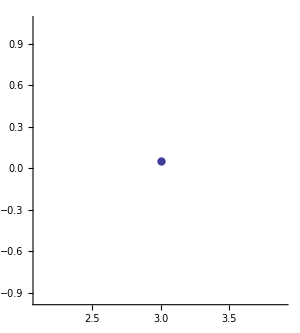

```mathematica
WolframAlpha["3",{{"NumberLine",1},"Content"}]
```

```mathematica
WolframAlpha["3",{{"BaseConversions",1},"Content"}]
```

11_2

```mathematica
WolframAlpha["3",{{"CharacterCode",1},"Content"}]
```

control-C
ASCII:       3(hex: 03  |  octal: 003  |  binary: 00000011)
Unicode:     U+0003(decimal: 3)
(basic Latin)

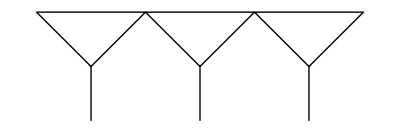
Roman | III
Greek | γ
Babylonian | -Graphics-
Mayan | -Graphics-

```mathematica
WolframAlpha["3",{{"RomanNumerals",1},"Content"},PodStates->{"RomanNumerals__Other historical numerals"}]
```

Interpretation of “three” or 3
The Signified - Resource

The Wolfram Language provides a uniform mechanism, the Interpreter function, for specifying how input of different types should be interpreted. Interpretations can involve either structural or semantic conversions. The strings that appear in $InterpreterTypes are the possible first arguments to Interpreter.

```mathematica
$InterpreterTypes//Short
```

{3DS,ACO,AdministrativeDivision,«606»,XYZ,ZIP,ZIPCode}

## Interpretation

Generally speaking interpretation is closely related with the assignment of meaning to any expression or concept. But in computer science an interpreter is a computer program that executes instructions. In Wolfram Language the interpreter is involved in the evaluation of an expression. In R3DM any interpretation is directly linked to the signified, the semantics of any information resource.

### The Interpreter Function

```mathematica
Interpreter["Number"]["3"]
(*returns the interpreted object only if applying test to it yields True;otherwise it returns a Failure object.*)
```

3

```mathematica
Interpreter["Number"]/@{3,"3",{3},"three"}
```

{3,3,{3},Failure[…]}

In the list above the last element cannot be interpreted as a number but according to Wolfram language the semantic interpretation should be tried instead. Indeed if we try

```mathematica
Interpreter["SemanticNumber"]["three"]
```

3

But if we try the semantic interpretation for the word three in Greek (τρία)

```mathematica
Interpreter["SemanticNumber"]["τρία"]
```

Failure[…]

### The Interpretation Function

How are we going to define our own interpretations ? Wolfram Language provides the interpretation function for that purpose.

#### Interpretation[e,expr]

Represents an object that :

displays as e

interpreted as the unevaluated form of expr if supplied as input

#### Interpretation of a unicode string e.g. “τρια” as 3

```mathematica
Interpretation["τρία",3]
```

τρία

```mathematica
%//StandardForm
```

τρία

```mathematica
%%//InputForm
```

Interpretation["τρία", 3]

```mathematica
%%%//OutputForm
```

Interpretation[τρία, 3]

```mathematica
%%%%//Head
```

Interpretation

In this example, the output of the Interpretation function is not a string, it evaluates to the expr argument, i.e the integer number 3.
Copy and paste that output when building expressions to display as a string in its unevaluated form.
When the custom expression is going to be evaluated the string will be interpreted as a number.

```mathematica
"τρία"
```

3

```mathematica
Head["τρία"]
```

Integer

#### Interpretation of a numeral e.g. “III” as 3

```mathematica
Interpretation["III",3]
```

III

```mathematica
%//Head
```

Interpretation

```mathematica
%%//OutputForm
```

Interpretation[III, 3]

```mathematica
%%%//StandardForm
```

III

```mathematica
%%%%//InputForm
```

Interpretation["III", 3]

```mathematica
"III"
```

3

```mathematica
%//Head
```

Integer

#### String vs Interpretation

In order to demonstrate the difference we will input a string expression with the keyboard first as the argument of the Head function

```mathematica
Head["III"]
```

String

then we will copy and paste the output of the previous interpretation expression, i.e. "III", as the argument of the Head function

```mathematica
Head["III"]
```

Integer

Now let us try the same using the Interpreter function with a string argument type

```mathematica
Interpreter["String"]["III"]
```

III

```mathematica
Interpreter["String"]["III"]
```

Failure[…]

```mathematica
Interpreter["Number"]["III"]
```

3

#### Evaluation of an expression with user-defined interpretations

```mathematica
3*"τρία"-2*"III"
```

3

```mathematica
NumberQ/@{"III","τρία"}
```

{True,True}

Storage of ‘3’
The Signifier - Realization

We will end our discussion on the three-faceted abstraction mechanism that we use for number ‘3’ with the analysis of data types and encoding, decoding mechanisms to store various representations of ‘3’. First we will compare atomic and complex data types. We can view data types as containers of a specific type of content.

## The Container-Content Duality

### Container (Form)

#### Integer Container (Data Type)

```mathematica
Head[3]
```

Integer

#### String Container (Data Type)

```mathematica
Head["3"]
```

String

#### List Container (Data Type)

```mathematica
Head[{3}]
```

List

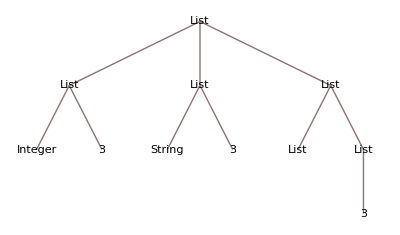

```mathematica
{
{Head[3],3},
{Head["3"],"3"},
{Head[{3}],{3}}
} //TreeForm
```

```mathematica
AtomQ/@{Three,three,"three",3,"3",{3}}
```

{True,True,True,True,True,False}

```mathematica
{True,True,False,}
```

{True,True,False,Null}

### Content (Value)

Second, in Mathematica the content, i.e. the value can be assigned to a variable or a constant in two different ways.

#### Symbol replacement (variable)

```mathematica
Rule[a,3]
```

a→3

```mathematica
ReplaceAll[2a-3,a->3]
```

3

#### Symbol name (constant)

```mathematica
a=3
```

3

```mathematica
2a-3
```

3

## Encoding and Decoding of Container-Content

We continue our discussion with two different kinds of container - content. The first one is an Image container (symbol) realized in Mathematica as a raw array of bytes, and the second is a Sound container (symbol) realized in Mathematica as a list of sound amplitude levels samples. Do notice that both visual and aural representations have not been assigned any interpretation.

### Image of 3 - Visual Representation

This is an image of number 3. It depicts the Western Arabic numeral of the digit ‘3’.

```mathematica
-Graphics-//FullForm
```

Image[RawArray["Byte",List[List[List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],67,List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255],List[255,255,255]],86]],4,Rule[1]]
 |  |  |  |

```mathematica
img3=%;
```

```mathematica
img3//Head
```

Image

#### 8-bit Encoding

```mathematica
img3//InputForm//Short
```

Image[RawArray[Byte, {{{255, 255, 255}, {255, 255, 255}, {<<3>>}, <<83>>, {255, 255, 255}}, <<86>>}], <<5>>]

```mathematica
img3//ByteCount
```

28907

```mathematica
img3string=ToString[img3,StandardForm]
```

…

```mathematica
img3string//Head
```

String

```mathematica
img3string//FullForm//Short
```

"\*GraphicsBox[TagBox[RasterBox[RawArray["Byte", List[Li"\[Ellipsis]" 87], List[0, 87]]], Rule[ImageSize, Magnification[1]]]\)"

64-bit (double-precision real) Encoding

```mathematica
img3//ImageType
```

Byte

```mathematica
Image[ImageData[img3,"Real"][[20;;40,30;;45]]]
```

-Graphics-

```mathematica
ImageData[img3,"Real"][[20;;40,30;;45]][[1]]
```

{{0.00392157,0.521569,0.854902},{0.,0.517647,0.847059},{0.00392157,0.521569,0.85098},{0.,0.517647,0.85098},{0.,0.513725,0.847059},{0.,0.509804,0.847059},{0.,0.509804,0.843137},{0.,0.505882,0.835294},{0.,0.501961,0.831373},{0.00784314,0.521569,0.862745},{0.0117647,0.513725,0.847059},{0.0156863,0.486275,0.807843},{0.0156863,0.470588,0.780392},{0.0156863,0.470588,0.780392},{0.0117647,0.486275,0.807843},{0.00784314,0.517647,0.858824}}

#### Base64 String Encoding

```mathematica
img3b64=ExportString[img3,{"Base64","JPEG"}];
```

```mathematica
img3b64//Short
```

/9j/4AAQSkZJRgABAQEASABIAAD/4QEkRXhpZgAATU0AKgAAAAgACwESAA…cZooqiRpWk20UUxCeWKXy6KKCbCh
KkCUUUwHBaXFFFIpCiiiikM//9k=

Another image for number 3. This one has a connotation, because it depicts three fingers which is not a glyph for a numeral.

### Speech sound of 3 - Aural Representation

#### MP3 Encoding

```mathematica
snd3=Import["https://ssl.gstatic.com/dictionary/static/sounds/de/0/three.mp3"]
```

-Graphics-

```mathematica
EmitSound[snd3]
```

```mathematica
snd3//Head
```

Sound

```mathematica
snd3//FullForm
```

Sound[SampledSoundList[List[List[0.,0.,0.,0.,0.,0.,0.,0.,14384,-0.0000592805,0.0000139214,0.0000155643,0.00013081,0.0000990741,0.00011709,0.0000665523,-0.0000893362]],22050]]
 |  |  |  |

#### 8bit Encoding for Sound Amplitude Levels

```mathematica
ListPlay[snd3[[1]][[1]][[1]][[4000;;10000]],SampleRate->16000,SampleDepth->8]
```

-Graphics-

```mathematica
snd3[[1]][[1]][[1]][[4000;;10000]]//Short
```

{-0.0426587,-0.00663353,«5998»,0.146392}

#### WAV Encoding

```mathematica
Export["three.wav",snd3,"WAV"]
```

three.wav